```mathematica
ClearAll["Global`*"];
```

```mathematica
(* Compute pf ev*)
getPF[mat_]:=Module[
(*returns eigenvector of largest eigenvalue*)
{vals,vecs},
{vals,vecs}=Eigensystem[mat]//N;
Normalize[vecs[[Ordering[vals,-1]]][[1]],Total]
]
```

```mathematica
(* Adjusted adjacency matrix *)
A={{0,1,0},{0,0,1},{-1,-1,0}};
A//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-1 | -1 | 0)

```mathematica
(* Adjacency matrix *)
adja=Transpose[Abs[A]];
adja//MatrixForm

adjaPF=getPF[adja];
adjaPF
```

(0 | 0 | 1
1 | 0 | 1
0 | 1 | 0)

{0.245122,0.43016,0.324718}

```mathematica
(* Visualization *)
edgeLabels=Flatten[Table[Table[If[adja[[i]][[j]]≠0,(i->j)->Style[If[A[[j]][[i]]>0,"+","-"],Bold,40],##&[]],{j,1,3}],{i,1,3}]];
AdjacencyGraph[adja,VertexLabels->Table[(i+1)->Style[i,20],{i,0,2}],EdgeLabels->edgeLabels]
```

-Graphics-

```mathematica
(* Analysis *)
f1[x_]:=1/(1+x)
f2[x_]:=x/(1+x)

x={x0,x1,x2}; (*RandomReal[{0,1},3]*)

xd[i_]:=e1*Sum[1/2*(Abs[A[[i+1]][[j+1]]]-A[[i+1]][[j+1]])*f1[x[[j+1]]],{j,0,2}]+e2*Sum[1/2*(Abs[A[[i+1]][[j+1]]]+A[[i+1]][[j+1]])*f2[x[[j+1]]],{j,0,2}];

xd[0]
xd[1]
xd[2]
```

(e2 x1)/(1+x1)

(e2 x2)/(1+x2)

e1 (1/(1+x0)+1/(1+x1))

```mathematica
(* Jacobian *)
J=D[{xd[0],xd[1],xd[2]},{x}];
J//MatrixForm
```

(0 | -(e2 x1)/(1+x1)^2+e2/(1+x1) | 0
0 | 0 | -(e2 x2)/(1+x2)^2+e2/(1+x2)
-e1/(1+x0)^2 | -e1/(1+x1)^2 | 0)

```mathematica
(* at steady state *)
steadyState={0.41400003,0.72651834,0.54842964}; (*from adja_m multiplication*)

Jv=J/.{x0->steadyState[[1]],x1->steadyState[[2]],x2->steadyState[[3]]};
Jv=Jv/.{e1->0.1,e2->0.9};
Jv//MatrixForm

{vals,vecs}=Eigensystem[Jv]//N
```

(0 | 0.301926 | 0
0 | 0 | 0.37537
-0.0500151 | -0.0335473 | 0)

{{0.0774567+0.174904 ⅈ,0.0774567-0.174904 ⅈ,-0.154913},{{0.814968+0. ⅈ,0.209074+0.472106 ⅈ,-0.176836+0.194836 ⅈ},{0.814968+0. ⅈ,0.209074-0.472106 ⅈ,-0.176836-0.194836 ⅈ},{-0.874341,0.448611,-0.185139}}}

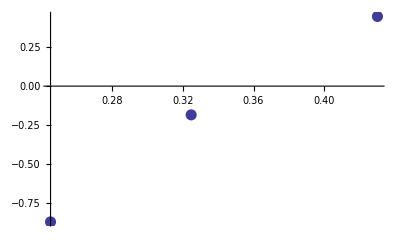

```mathematica
(* Compare systems *)
adjaPF;
jacoPF=vecs[[3]];(*eivec of largest real eival*)

ListPlot[Thread[{adjaPF,jacoPF}],PlotStyle->PointSize[0.02]]
```